```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/robyn/Documents/Research/KLStats/Isochrone/WithGaiaErrors/MSTO

```mathematica
<<streams10x5000.mx
```

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Define the “true” potential

```mathematica
Phi[r_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])
PhiEff[r_,L_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])+L^2/(2 r^2)
vcirc[r_,M_,b_]:=Sqrt[(M r^2)/(Sqrt[b^2+r^2] (b+Sqrt[b^2+r^2])^2)]
```

```mathematica
Jr[r_,pr_,L_,M_,b_]:=M/Sqrt[-pr^2-L^2/r^2+2 M/(b+Sqrt[b^2+r^2])]-1/2 (L+Sqrt[L^2+4 M b]/2)
```

Color point plots

```mathematica
ListColorPlot[x_,y_,c_,csize_,cscl_,xlab_,ylab_]:=Show[Graphics[Flatten[MapThread[{ColorData[cscl][(#3-Min[c])/(Max[c]-Min[c])],Disk[{#1,#2},csize]}&,{x,y,c}]]],Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],FrameLabel->{xlab,ylab}]
```

Annotation for the color plot - shows a color bar

```mathematica
PlotAnnotate[M_,b_,crange_,dc_,label_]:=Graphics[{Style[Text["M = "<>ToString[M]<>" \!\(\*SuperscriptBox[\(kpc\), \(3\)]\)\!\(\*SuperscriptBox[\(Myr\), \(-2\)]\), b="<>ToString[b]<>" kpc",Scaled[{0.02,0.98}],{-1,1}],TextAlignment->-1,FontFamily->"Helvetica",FontSize->18],MyColorBar[crange,dc,label][[1]]}]

α=0.9;(*total scaled width of color bar*)
β=0.05;(*scaled offset from the left end of the plot*)
γ=0.05;(*scaled distance of the bottom of the bar from the bottom of the plot*)
δγ=0.03;(*scaled height of color bar*)MyColorBar[crange_,dc_,label_]:=Graphics[Flatten[{Black,Style[Text[label,Scaled[{β/2,γ+δγ/2}]],FontFamily->"Helvetica",FontSize->14],Table[{ColorData["Rainbow"][(c-crange[[1]])/(crange[[2]]-crange[[1]])],Rectangle[Scaled[{α (c-crange[[1]])/(crange[[2]]+dc-crange[[1]])+β,γ}],Scaled[{α (c-crange[[1]]+dc)/(crange[[2]]+dc-crange[[1]])+β,γ+δγ}]],Black,Style[Text[Round[c,dc],Scaled[{α (c-crange[[1]]+dc/2)/(crange[[2]]+dc-crange[[1]])+β,γ+1.75 δγ}]],FontFamily->"Helvetica",FontSize->14]},{c,crange[[1]],crange[[2]],dc}]}]]
```

```mathematica
MyColorBar[{0,10},1,"J_r"]
```

Examine distances from the Sun to the stream stars

```mathematica
trueDists=Sqrt[(truePositions[[All,1]]-8)^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

```mathematica
dbins=Table[id,{id,0,80,1}];
dcounts=BinCounts[trueDists,{dbins}];
```

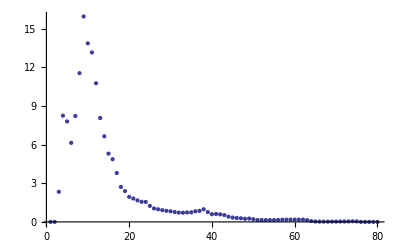

```mathematica
ListPlot[Transpose[{dbins[[2;;Length[dbins]]],dcounts/(dbins[[2;;Length[dbins]]]^2)}],PlotRange->All]
```

Convert (x,v) to observables, convolve with errors, and convert back to (x’,v’)

NOTE: make sure that these four filenames are the same in here and in data_realization_gaia.f!!!!

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
```

OutputStream[pos.test.dat,109]

OutputStream[vel.test.dat,110]

```mathematica
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.test.dat

vel.test.dat

## At this point, manually run data_realizations_gaia

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

50000

50000

{50000,3}

{50000,3}

{50000,11}

columns of observational file are vmag, alpha, delta, parallax, par error, mu_alpha, pm error, mu_delta, pm error, RV, RV error

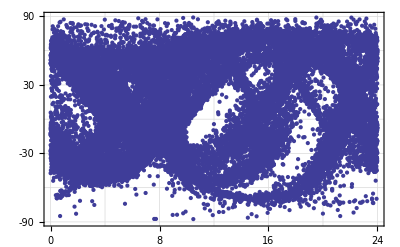

```mathematica
ListPlot[Transpose[{convObs[[All,2]]*24/(2π),convObs[[All,3]]/Degree}],PlotRange->{{0,24},{-90,90}},Frame->True,FrameTicks->{Range[0,24,4],Range[-90,90,30],None,None},GridLines->{Range[0,24,4],Range[-90,90,30]}]
```

Data quality cuts (on observational data)

### Histogram of magnitudes - cut out V>20

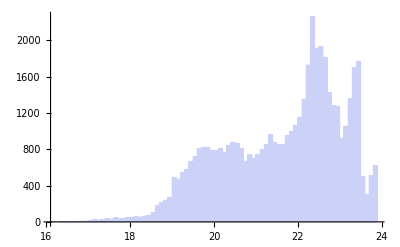

```mathematica
Histogram[convObs[[All,1]]]
```

```mathematica
Tally[magSel=Thread[convObs[[All,1]]<20]]
```

{{True,48072},{False,1928}}

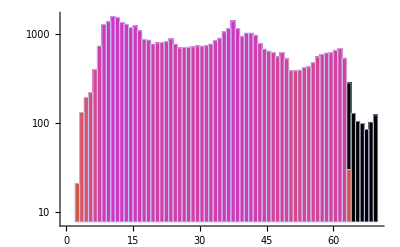

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Cut out negative parallaxes, and those with huge errors

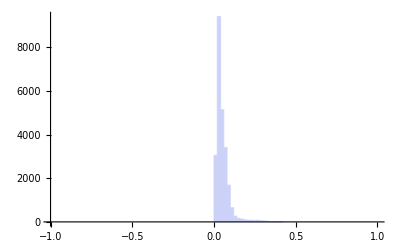

```mathematica
Histogram[convObs[[All,4]],{-1,1,.02}]
```

```mathematica
Tally[posParSel=Thread[Thread[(convObs[[All,4]]>1*^-5)]&&Thread[(convObs[[All,4]]<10)]]]
```

{{False,41624},{True,8376}}

```mathematica
pars=Pick[convObs[[All,4]],posParSel];
```

```mathematica
pars[[Ordering[pars,-50]]]
```

{0.302387,0.303394,0.304265,0.304701,0.304747,0.305393,0.306521,0.307151,0.307293,0.309028,0.309384,0.309528,0.309632,0.312099,0.313439,0.313877,0.313994,0.315543,0.31564,0.31692,0.322493,0.323117,0.323566,0.324814,0.326842,0.330475,0.334853,0.336861,0.33803,0.339671,0.341241,0.342175,0.345335,0.347169,0.348216,0.358516,0.361141,0.365271,0.37023,0.372767,0.38101,0.384023,0.386032,0.391621,0.413205,0.420558,0.42403,0.428778,0.47284,0.473592}

Histogram::hbins: The bin specification {"Log", {-5, 0, 0.1}} cannot be used to determine either how many or which bins to use.

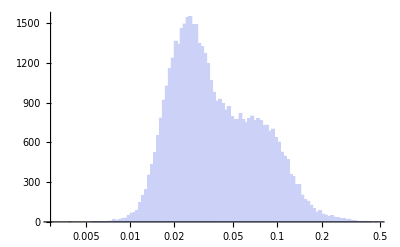

```mathematica
Histogram[Pick[convObs[[All,4]],posParSel],{"Log",{-5,0,0.1}}]
```

```mathematica
Tally[hugeParErrSel=Thread[Abs[convObs[[All,5]]]< 1000]]
```

{{False,41647},{True,8353}}

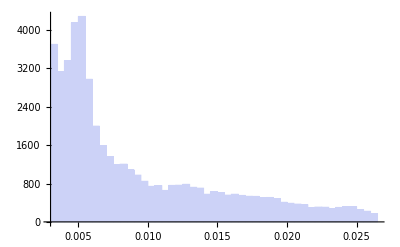

```mathematica
Histogram[Pick[convObs[[All,5]],hugeParErrSel],PlotRange->All]
```

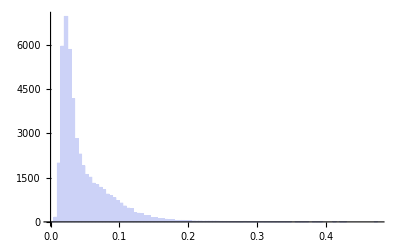

```mathematica
Histogram[Pick[convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],PlotRange->All]
```

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

-Graphics-

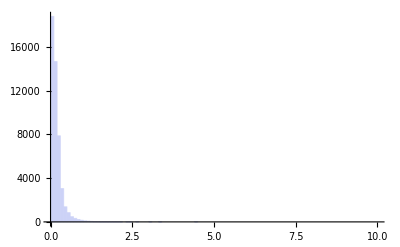

```mathematica
Histogram[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],{0,10,0.1}]
```

```mathematica
Log10[Max[trueDists]]
```

1.82856

```mathematica
Log10[Min[trueDists]]
```

0.312347

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]],Sin[Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]],Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],.02,"Rainbow","α","Sin δ"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

-4.25026

```mathematica
Max[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

3.21689

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]],1,"Rainbow","RA","Dec"],MyColorBar[{-4.25,3.25},0.25,"σ_D/D"]]
```

-Graphics-

```mathematica
Log10[Min[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

-1.15366

```mathematica
Log10[Max[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

3.95239

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{-1.15,4.0},0.5,"σ_π/π"]]
```

-Graphics-

### Dataquality cut on parallaxes

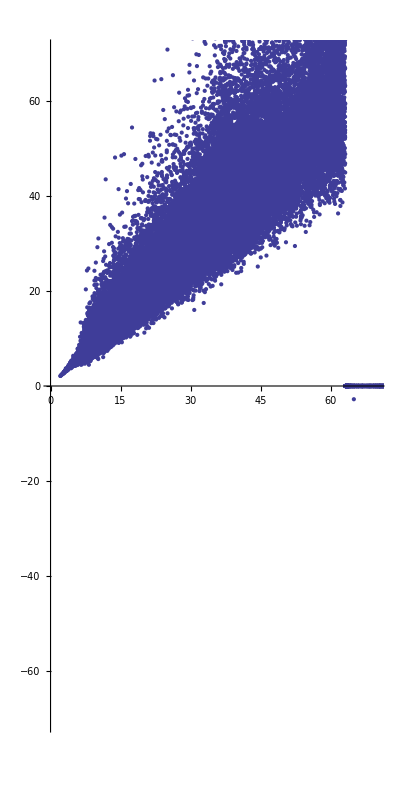

```mathematica
ListPlot[Transpose[{trueDists,1/convObs[[All,4]]}],PlotRange->{{0,70},{-70,70}},AspectRatio->2]
```

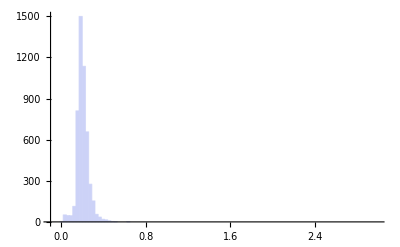

```mathematica
Histogram[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]],{-.1,3,.03}]
```

```mathematica
Tally[dqParSel=Thread[Abs[convObs[[All,5]]/convObs[[All,4]]]<0.2]]
```

{{False,45817},{True,4183}}

```mathematica
4183./50000
```

0.08366

```mathematica
Dimensions[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]
```

{24529}

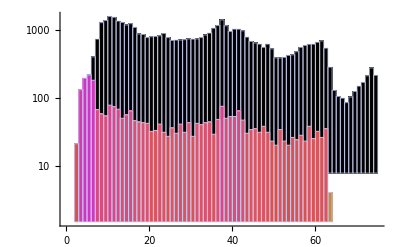

```mathematica
Show[Histogram[trueDists,{0,75,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]],{0,75,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.386366

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.79517

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.312347

```mathematica
Max[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.79998

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.3,1.8},0.1,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.311351

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.7888

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.3,1.8},0.1,"[1/π]"]]
```

-Graphics-

### Dataquality cut on proper motions is basically the same as for pars - errors are proportional

### Dataquality cut on RVs

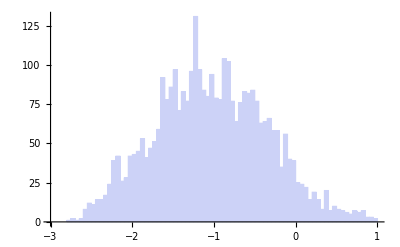

```mathematica
Histogram[Log10[convObs[[All,11]]/convObs[[All,10]]],{-3,1,.05}]
```

```mathematica
Tally[dqRVSel=Thread[Abs[convObs[[All,11]]]<10]]
```

{{False,49919},{True,81}}

```mathematica
81./50000
```

0.00162

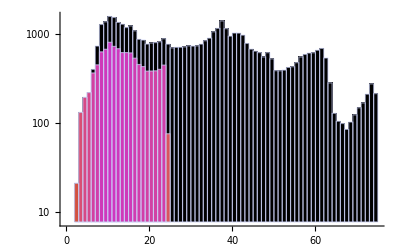

```mathematica
Show[Histogram[trueDists,{0,75,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]],{0,75,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Combining all the cuts together

```mathematica
Tally[allSels=Thread[posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]]
```

{{False,49945},{True,55}}

```mathematica
55./50000
```

0.0011

```mathematica
Dimensions[tpSel=Pick[truePositions,allSels]]
```

{7775,3}

```mathematica
Dimensions[cpSel=Pick[convPositions,allSels]]
```

{7775,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,allSels]]
```

{7775,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,allSels]]
```

{7775,3}

### Plots examining error behavior etc

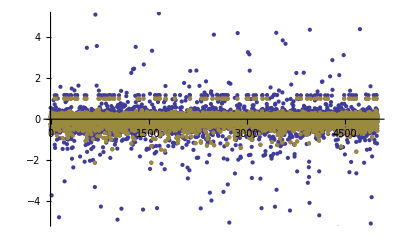

```mathematica
ListPlot[Transpose[(truePositions-convPositions)/truePositions],PlotRange->{-5,5}]
```

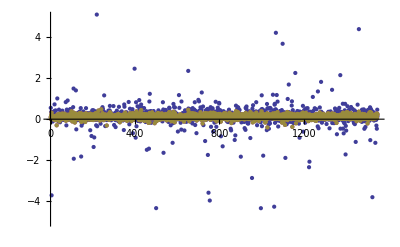

```mathematica
ListPlot[Transpose[(tpSel-cpSel)/tpSel],PlotRange->{-5,5}]
```

```mathematica
convDists=Sqrt[(convPositions[[All,1]]-8)^2+convPositions[[All,2]]^2+convPositions[[All,3]]^2];
```

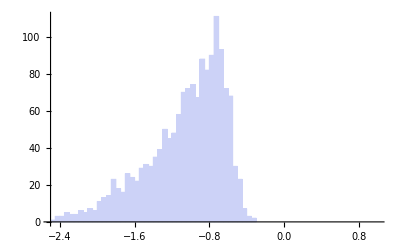

```mathematica
Histogram[Pick[Log10[Abs[(trueDists-convDists)]/trueDists],allSels],{-2.5,1,0.05}]
```

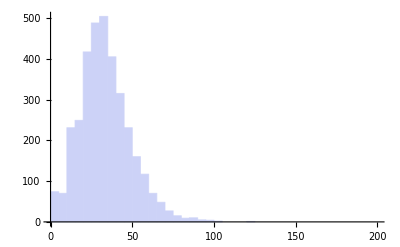

```mathematica
Histogram[Pick[convDists,Thread[!allSels]],{0,200,5}]
```

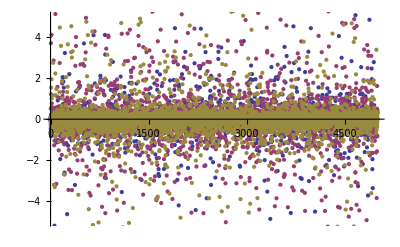

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

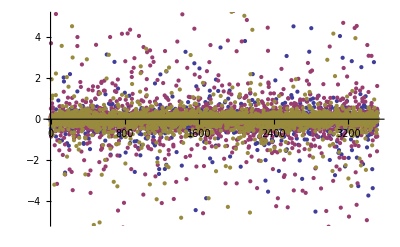

```mathematica
ListPlot[Transpose[(tvSel-cvSel)/tvSel],PlotRange->{-5,5}]
```

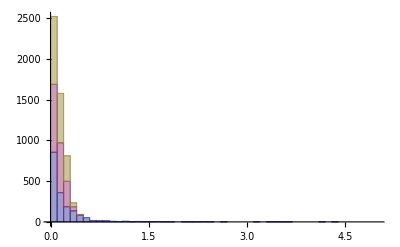

```mathematica
Histogram[Transpose[(tpSel-cpSel)/tpSel],{0,5,.1},ChartLayout->"Stacked"]
```

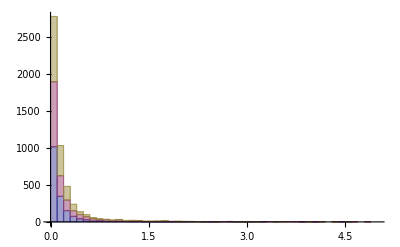

```mathematica
Histogram[Transpose[(tvSel-cvSel)/tvSel],{0,5,.1},ChartLayout->"Stacked"]
```

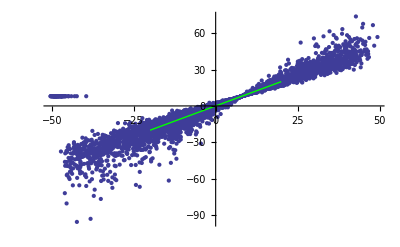

```mathematica
Show[ListPlot[Transpose[{truePositions[[All,1]],convPositions[[All,1]]}]],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

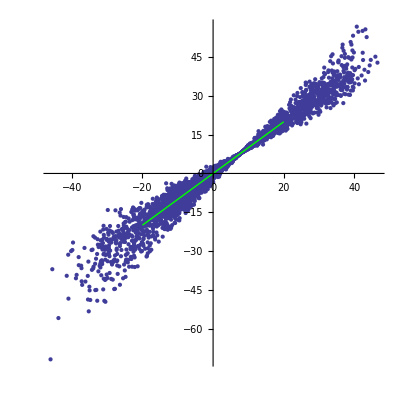

```mathematica
Show[ListPlot[Transpose[{tpSel[[All,1]],cpSel[[All,1]]}],AspectRatio->1],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

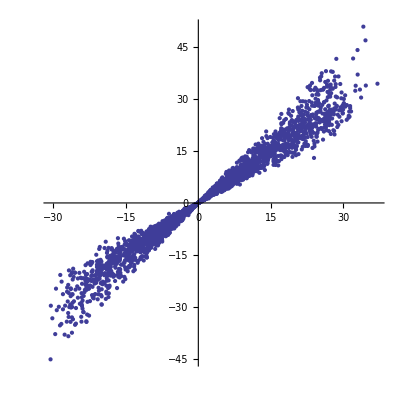

```mathematica
ListPlot[Transpose[{tpSel[[All,2]],cpSel[[All,2]]}],AspectRatio->1]
```

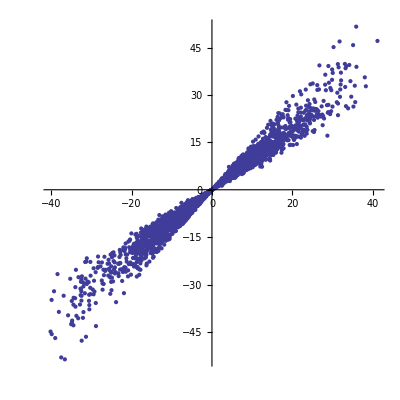

```mathematica
ListPlot[Transpose[{tpSel[[All,3]],cpSel[[All,3]]}],AspectRatio->1]
```

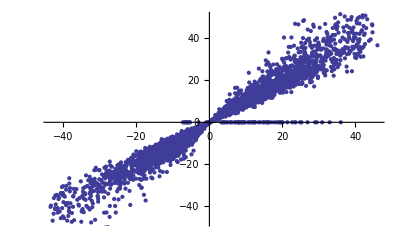

```mathematica
ListPlot[Transpose[{truePositions[[All,3]],convPositions[[All,3]]}]]
```

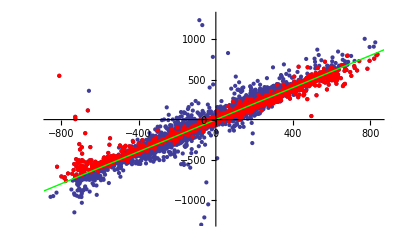

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,1]],convVelocities[[All,1]]}]],ListPlot[Transpose[{tvSel[[All,1]],cvSel[[All,1]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

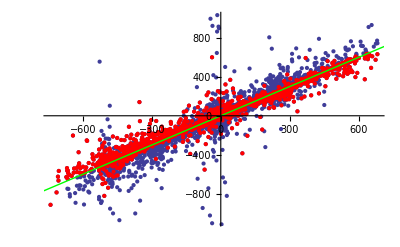

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,2]],convVelocities[[All,2]]}]],ListPlot[Transpose[{tvSel[[All,2]],cvSel[[All,2]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

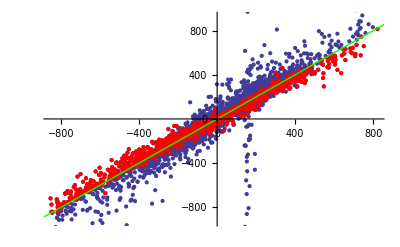

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,3]],convVelocities[[All,3]]}]],ListPlot[Transpose[{tvSel[[All,3]],cvSel[[All,3]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

Convert (x’,v’) to (Jr’,L’,Lz’) using the input params

```mathematica
fnameCleanPosIn="pos.clean.dat"
fnameCleanVelIn="vel.clean.dat"
```

pos.clean.dat

vel.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[pos.clean.dat,54]

OutputStream[vel.clean.dat,55]

```mathematica
Write[pStream,Length[cpSel]];
Export[pStream,cpSel,"Data"];
Export[vStream,cvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.clean.dat

vel.clean.dat

```mathematica
link=Install["/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]
```

LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,3537,9]

```mathematica
Mtrial=12.2;
btrial=8.0;
```

```mathematica
Dimensions[convJ=Table[{0,0,0},{i,1,Length[cpSel]}]]
```

{7775,3}

```mathematica
For[i=1,i≤Length[cpSel],i++,convJ[[i]]=CartToAA[Mtrial,btrial,cpSel[[i]],cvSel[[i]]];];
```

Some stuff has unbound orbits, so select those out

```mathematica
Tally[boundSel=Thread[convJ[[All,3]]>0]]
```

{{False,2002},{True,5773}}

```mathematica
Dimensions[convJbound=Pick[convJ,boundSel]]
```

{5773,3}

```mathematica
Dimensions[tJSel=Pick[Pick[trueActions,allSels],boundSel]]
```

{5773,3}

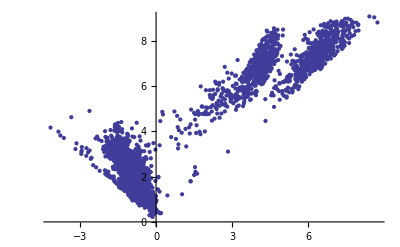

```mathematica
ListPlot[convJbound[[All,{1,2}]]]
```

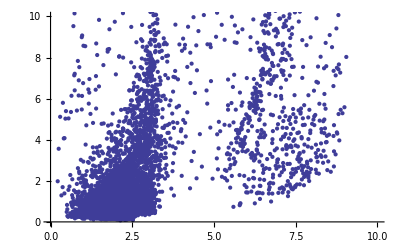

```mathematica
ListPlot[convJbound[[All,{2,3}]],PlotRange->{{0,10},{0,10}}]
```

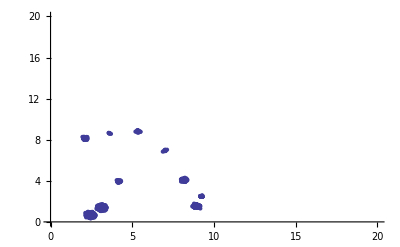

```mathematica
ListPlot[tJSel[[All,{2,3}]],PlotRange->{{0,20},{0,20}}]
```

```mathematica
ListPointPlot3D[convJbound]
```

-Graphics3D-

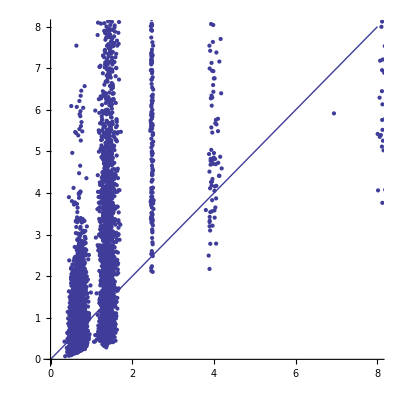

```mathematica
Show[ListPlot[Transpose[{tJSel[[All,3]],convJbound[[All,3]]}],PlotRange->{{0,8},{0,8}},AspectRatio->1],Plot[x,{x,0,8}]]
```

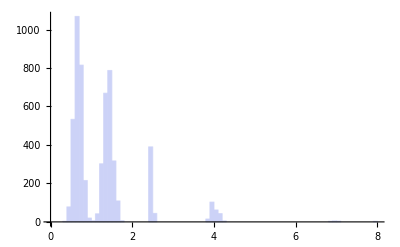

```mathematica
Histogram[tJSel[[All,3]],{0,8,.1}]
```

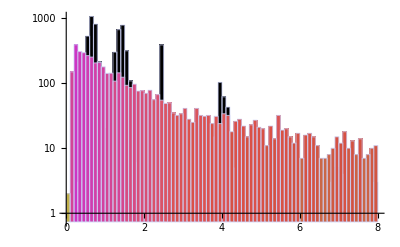

```mathematica
Show[Histogram[tJSel[[All,3]],{0,8,.1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[convJbound[[All,3]],{0,8,.1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

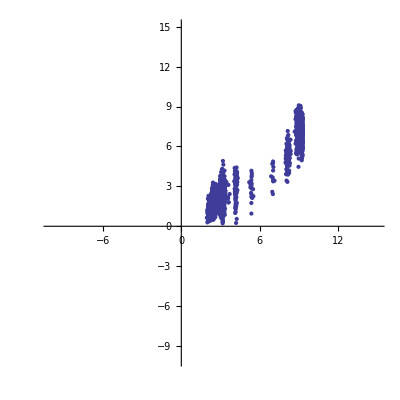

```mathematica
ListPlot[Transpose[{tJSel[[All,2]],convJbound[[All,2]]}],PlotRange->{{-10,15},{-10,15}},AspectRatio->1]
```

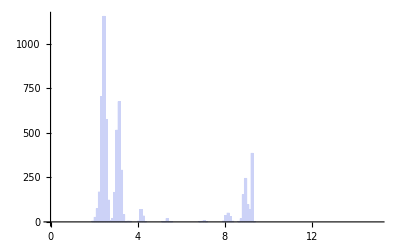

```mathematica
Histogram[tJSel[[All,2]],{0,15,.1}]
```

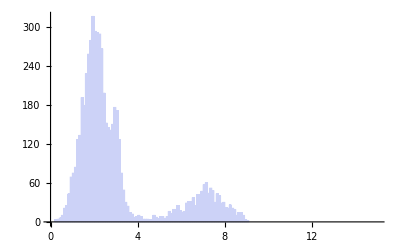

```mathematica
Histogram[convJbound[[All,2]],{0,15,.1}]
```

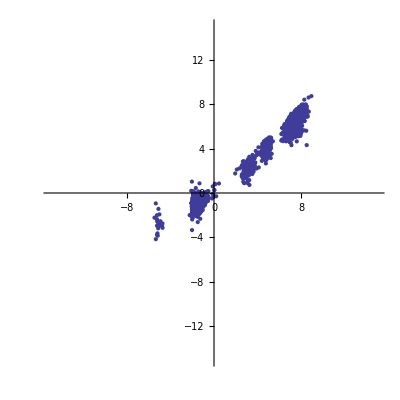

```mathematica
ListPlot[Transpose[{tJSel[[All,1]],convJbound[[All,1]]}],PlotRange->{{-15,15},{-15,15}},AspectRatio->1]
```

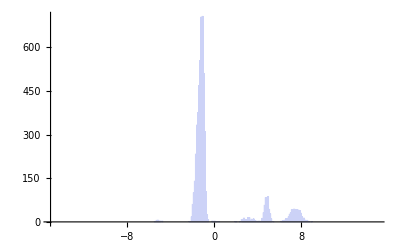

```mathematica
Histogram[tJSel[[All,1]],{-15,15,.1}]
```

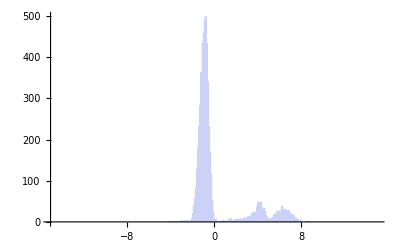

```mathematica
Histogram[convJbound[[All,1]],{-15,15,.1}]
```

Explore param space and generate KL map

```mathematica
Mt0=5.2;
bt0=1.0;
dM=1.0;
db=1.0;
MtMax=19.2;
btMax=16.0;
```

```mathematica
((MtMax-Mt0)/dM)((btMax-bt0)/db)
```

224.

```mathematica
Mtrial=5.2
btrial
```

5.2

8.

```mathematica
nNN=10;
```

```mathematica
trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions,goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=3 nNN/(4π allNN^3)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]],goodActions[[All,3]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=3nNN/(4π allNN^3)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]
```

1.89699

```mathematica
ListPointPlot3D[{goodActions,shuffL}]
```

-Graphics3D-

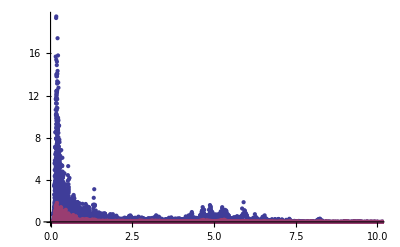

```mathematica
ListPlot[{Transpose[{Sort[goodActions[[All,3]]],trialSample[[Ordering[goodActions[[All,3]]]]]}],Transpose[{Sort[goodActions[[All,3]]],smoothSample[[Ordering[goodActions[[All,3]]]]]}]},PlotRange->{{0,10},All}]
```

```mathematica
ParallelEvaluate[$ProcessID]
```

{2650,2651}

```mathematica
ParallelEvaluate[$MachineName]
```

{theophilus,theophilus}

```mathematica
ParallelEvaluate[Install["/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]]
```

{LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,3,3],LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,3,3]}

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions,goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=3 nNN/(4π allNN^3)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]],goodActions[[All,3]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=3nNN/(4π allNN^3)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{45.6929,{240,3}}

```mathematica
KLStats[[100;;110]]
```

{{11.2,4.,1.89677},{11.2,5.,1.91511},{11.2,6.,1.99191},{11.2,7.,2.04629},{11.2,8.,2.16032},{11.2,9.,2.13593},{11.2,10.,2.08616},{11.2,11.,2.06597},{11.2,12.,2.01201},{11.2,13.,1.99197},{11.2,14.,1.93526}}

```mathematica
Max[KLStats[[All,3]]]
```

2.1709

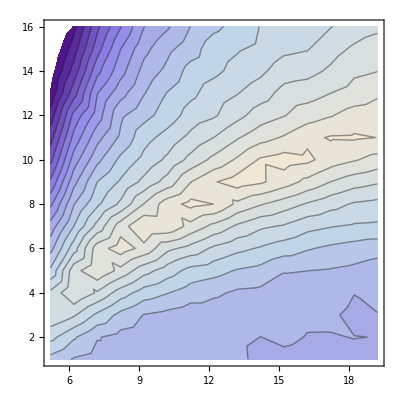

```mathematica
ListContourPlot[KLStats,Axes->True,AxesOrigin->{12.2,8.0},Contours->Range[0,2.2,0.05]]
```

```mathematica
DumpSave["KL10x5000Gaia.mx",KLStats];
```

```mathematica
5.2/4.5
19.2/4.5
```

1.15556

4.26667

Try a search in Log M instead

```mathematica
toSolarMasses=1/4.5*^-12
```

2.22222×10^11

```mathematica
logMt0=11.5;
bt0=1.0;
dlogM=0.1;
db=0.5;
logMtMax=14.5;
btMax=20.0;
```

```mathematica
((logMtMax-logMt0)/dlogM)((btMax-bt0)/db)
```

1140.

```mathematica
Mtrial=14.5;
btrial=8.0;
```

```mathematica
(10^Mtrial)/toSolarMasses
```

14.2302

```mathematica
trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions,goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=3 nNN/(4π allNN^3)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]],goodActions[[All,3]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=3nNN/(4π allNN^3)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]
```

1.2186

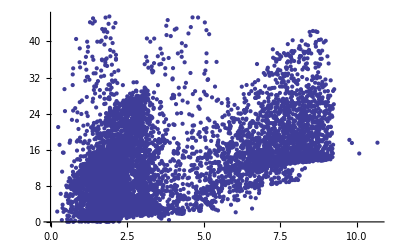

```mathematica
ListPlot[goodActions[[All,{2,3}]]]
```

```mathematica
nGood
```

7772

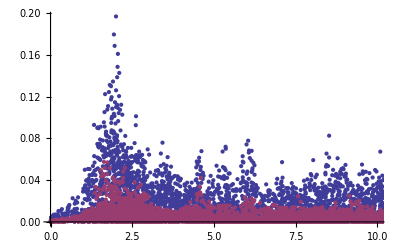

```mathematica
ListPlot[{Transpose[{Sort[goodActions[[All,3]]],trialSample[[Ordering[goodActions[[All,3]]]]]}],Transpose[{Sort[goodActions[[All,3]]],smoothSample[[Ordering[goodActions[[All,3]]]]]}]},PlotRange->{{0,10},All}]
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions,goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=3 nNN/(4π allNN^3)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]],goodActions[[All,3]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=3nNN/(4π allNN^3)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,logMt0,logMtMax,dlogM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{153.42,{1209,3}}

```mathematica
DumpSave["KL10x5000logM.mx",KLStats];
```

```mathematica
Max[KLStats[[All,3]]]
```

1.72804

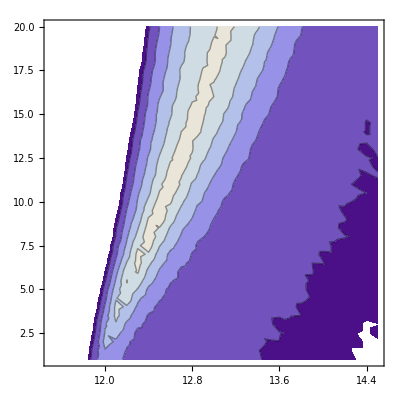

```mathematica
<<KL10x5000logM.mx
ListContourPlot[KLStats,Axes->True,AxesOrigin->{Log10[12.2 toSolarMasses],8.0},PlotRange->{1.2,1.75},Contours->Range[1.25,1.75,0.1]]
```

Try with only L and Jr not Lz

```mathematica
Mtrial=12.5;
btrial=20.0;
```

```mathematica
trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]
```

0.372058

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,logMt0,logMtMax,dlogM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{201.71,{1209,3}}

```mathematica
DumpSave["KL10x5000logM2D.mx",KLStats];
```

```mathematica
Max[KLStats[[All,3]]]
```

0.742099

Get::noopen: Cannot open "KL10x5000logM2D.mx".

$Failed

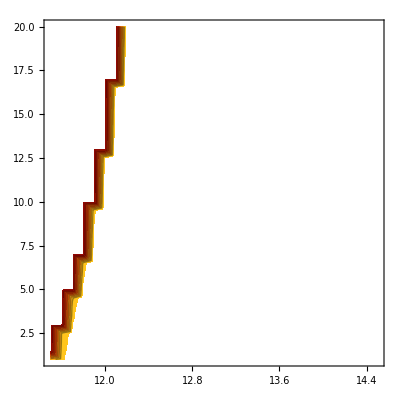

```mathematica
<<KL10x5000logM2D.mx
ListContourPlot[KLStats,Axes->True,AxesOrigin->{Log10[12.2 toSolarMasses],8.0},PlotRange->{0.05,0.75},Contours->Range[0.05,0.75,0.1],ColorFunction->"SolarColors",FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],Axes->True,AxesStyle->Thick]
```